```mathematica
U=wf^(2/3)*wc^(1/3)
```

wc^(1/3) wf^(2/3)

```mathematica
Pf=2;
Pc=0.4;
Inc=30;
```

```mathematica
Inc*(4*Pc/Pf-Pc)^-1
```

75.

```mathematica
Solve[D[U,wf]-Pf*lam==0,lam]
```

{{lam→(2 wc^(1/3))/(3 Pf wf^(1/3))}}

```mathematica
Solve[D[U,wc]-Pc*lam==0,lam]
```

{{lam→wf^(2/3)/(3 Pc wc^(2/3))}}

```mathematica
Solve[(2 wc^(1/3))/(3 Pf wf^(1/3))==wf^(2/3)/(3 Pc wc^(2/3)),wf]
```

{{wf→(2 Pc wc)/Pf}}

```mathematica
f=Inc-Pf*wf-Pc*Inc/(3 Pc)
```

(2 Inc)/3-Pf wf

```mathematica
Solve[f==0,wf]
```

{{wf→(2 Inc)/(3 Pf)}}

```mathematica
30/(3*0.4)
```

25.

```mathematica
2*30/3
```

20

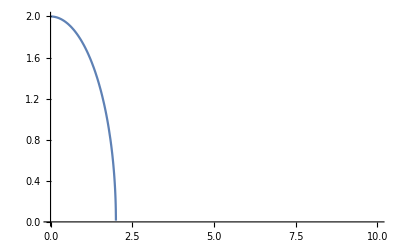

```mathematica
Plot[Sqrt[4-x^2],{x,0,10}]
```

```mathematica
Plot3D[Sqrt[y^2+x^2],{x,-20,20},{y,-20,20}]
```

-Graphics3D-

```mathematica
N[1-Sqrt[2/3]]
```

0.183503

```mathematica
N[Sqrt[2]]
```

1.41421

```mathematica
Simplify[(Inc - Pm*Inc/(2*Pc+Pm))1/Pc]
```

(2 Inc)/(2 Pc+Pm)